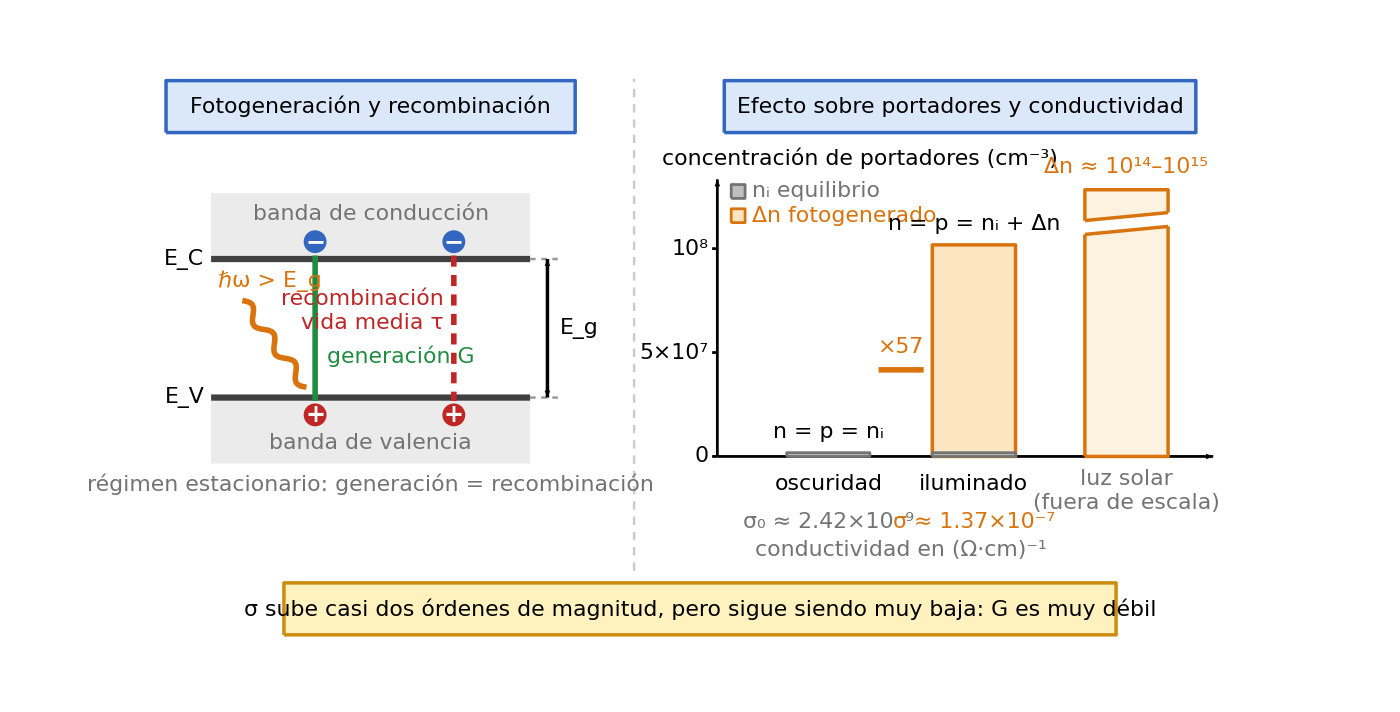

```mathematica
diagramaFotogeneracion = Module[
  {fs, mostrarValores, cAzul, cAzulB, cRojo, cVerde, cNar, cNarF, cGris, cOro, cOroB,
   e, ni, mun, mup, Gg, tau, dn, sig0, sig, fac, px, Lw, yC, yV, yh, ye,
   oxB, y0, sc, xo, xi, xs, ww, hb, pares, ins, insI, insD, caja, flecha, carga,
   onda, cient},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                 (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;   (* False oculta las conductividades y el factor de aumento *)
  cAzul  = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo  = RGBColor[0.75, 0.15, 0.15];  cVerde = RGBColor[0.13, 0.55, 0.25];
  cNar   = RGBColor[0.85, 0.45, 0.05];  cNarF  = RGBColor[0.99, 0.90, 0.76];
  cGris  = GrayLevel[0.45];
  cOro   = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Datos del problema (cm, V, s) ---------- *)
  e = 1.6*10^-19;  ni = 1.8*10^6;  mun = 8000;  mup = 400;
  Gg = 10^14;  tau = 10^-6;
  dn   = Gg tau;                       (* exceso fotogenerado *)
  sig0 = e ni (mun + mup);             (* conductividad en oscuridad *)
  sig  = e (ni + dn) (mun + mup);      (* conductividad iluminado *)
  fac  = Round[(ni + dn)/ni];          (* factor de aumento *)

  (* ---------- Geometría ---------- *)
  {px, Lw, yC, yV} = {2.4, 9.2, 7.2, 3.2};    (* diagrama de bandas *)
  {yh, ye} = {yV - 0.5, yC + 0.5};             (* alturas del hueco y del electrón *)
  {oxB, y0, sc} = {17.0, 1.5, 6./10^8};        (* gráfico de barras, escala lineal *)
  {xo, xi, xs, ww} = {20.2, 24.4, 28.8, 1.2};  (* centros y semianchura de las barras *)
  hb[c_] := sc c;

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  insD[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Right, Center}];
  flecha[p1_, p2_, col_, s_: 0.018] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  carga[pos_, signo_, col_] :=
    {col, Disk[pos, 0.33], Text[Style[signo, Round[1.1 fs], Bold, White], pos]};
  onda[p1_, p2_, amp_, ciclos_] := Module[{d, nv},
    d = p2 - p1;
    nv = {-d[[2]], d[[1]]}/Norm[d];
    Table[p1 + s d + amp Sin[2 Pi ciclos s] nv, {s, 0., 1., 0.01}]];
  cient[x_] := Module[{ex = Floor[Log10[x]]},
    Row[{NumberForm[x/10.^ex, {3, 2}], "×", Superscript["10", ex]}]];
  pares = {{0, "0"},
    {5*10^7, Row[{5, "×", Superscript["10", 7]}]},
    {10^8, Superscript["10", 8]}};

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* cabeceras y separador *)
    caja[{7.0, 11.6}, {11.8, 1.5}, cAzul, cAzulB],
    ins["Fotogeneración y recombinación", {7.0, 11.6}],
    caja[{24.0, 11.6}, {13.6, 1.5}, cAzul, cAzulB],
    ins["Efecto sobre portadores y conductividad", {24.0, 11.6}],
    {GrayLevel[0.8], AbsoluteThickness[1.8], AbsoluteDashing[{6, 5}],
     Line[{{14.6, -1.8}, {14.6, 12.4}}]},

    (* ===== Panel izquierdo: bandas de energía ===== *)
    {GrayLevel[0.92], EdgeForm[None],
     Rectangle[{px, yC}, {px + Lw, yC + 1.9}],
     Rectangle[{px, yV - 1.9}, {px + Lw, yV}]},
    {GrayLevel[0.25], AbsoluteThickness[4.5],
     Line[{{px, yC}, {px + Lw, yC}}], Line[{{px, yV}, {px + Lw, yV}}]},
    ins["banda de conducción", {px + Lw/2, yC + 1.3}, cGris],
    ins["banda de valencia", {px + Lw/2, yV - 1.3}, cGris],
    insD[Row[{Subscript["E", "C"]}], {px - 0.2, yC}],
    insD[Row[{Subscript["E", "V"]}], {px - 0.2, yV}],

    (* banda prohibida *)
    {GrayLevel[0.6], AbsoluteThickness[1.8], AbsoluteDashing[{4, 4}],
     Line[{{px + Lw, yC}, {12.4, yC}}], Line[{{px + Lw, yV}, {12.4, yV}}]},
    {Black, AbsoluteThickness[2.5], Arrowheads[{-0.012, 0.012}],
     Arrow[{{12.1, yV}, {12.1, yC}}]},
    insI[Row[{Subscript["E", "g"]}], {12.45, (yC + yV)/2}],

    (* fotón y generación de un par electrón-hueco *)
    {cNar, AbsoluteThickness[4], Arrowheads[0.018],
     Arrow[onda[{3.3, 6.0}, {5.15, 3.5}, 0.16, 3]]},
    insI[Row[{"ℏω", " > ", Subscript["E", "g"]}], {2.6, 6.55}, cNar],
    carga[{5.4, ye}, "−", cAzulB],
    carga[{5.4, yh}, "+", cRojo],
    flecha[{5.4, yh + 0.4}, {5.4, ye - 0.4}, cVerde],
    insI[Row[{"generación ", Style["G", Italic]}], {5.75, 4.4}, cVerde],

    (* recombinación de otro par *)
    carga[{9.4, ye}, "−", cAzulB],
    carga[{9.4, yh}, "+", cRojo],
    {cRojo, AbsoluteThickness[4], AbsoluteDashing[{8, 6}], Arrowheads[0.018],
     Arrow[{{9.4, ye - 0.4}, {9.4, yh + 0.4}}]},
    insD[Column[{"recombinación",
       Row[{"vida media ", Style["τ", Italic]}]}, Right], {9.1, 5.7}, cRojo],
    ins["régimen estacionario: generación = recombinación",
     {px + Lw/2, 0.7}, cGris],

    (* ===== Panel derecho: concentración de portadores ===== *)
    {Black, AbsoluteThickness[2], Arrowheads[0.016],
     Arrow[{{oxB, y0}, {31.3, y0}}], Arrow[{{oxB, y0}, {oxB, 9.5}}]},
    insI[Row[{"concentración de portadores (", Superscript["cm", "−3"], ")"}],
     {15.4, 10.1}],
    Table[{Black, AbsoluteThickness[2],
      Line[{{oxB - 0.15, y0 + hb[pr[[1]]]}, {oxB, y0 + hb[pr[[1]]]}}],
      insD[pr[[2]], {oxB - 0.25, y0 + hb[pr[[1]]]}]}, {pr, pares}],

    (* leyenda *)
    {GrayLevel[0.75], EdgeForm[{AbsoluteThickness[2], cGris}],
     Rectangle[{17.4, 8.95}, {17.8, 9.35}]},
    insI[Row[{Subscript["n", "i"], " equilibrio"}], {18.0, 9.15}, cGris],
    {cNarF, EdgeForm[{AbsoluteThickness[2], cNar}],
     Rectangle[{17.4, 8.25}, {17.8, 8.65}]},
    insI[Row[{"Δ", Style["n", Italic], " fotogenerado"}],
     {18.0, 8.45}, cNar],

    (* barra en oscuridad *)
    {EdgeForm[{AbsoluteThickness[2], cGris}], GrayLevel[0.75],
     Rectangle[{xo - ww, y0}, {xo + ww, y0 + hb[ni]}]},
    ins[Row[{"n = p = ", Subscript["n", "i"]}], {xo, y0 + hb[ni] + 0.6}],
    ins["oscuridad", {xo, y0 - 0.8}],

    (* barra iluminado: equilibrio + exceso fotogenerado *)
    {EdgeForm[{AbsoluteThickness[2.5], cNar}], cNarF,
     Rectangle[{xi - ww, y0}, {xi + ww, y0 + hb[ni + dn]}]},
    {EdgeForm[{AbsoluteThickness[2], cGris}], GrayLevel[0.75],
     Rectangle[{xi - ww, y0}, {xi + ww, y0 + hb[ni]}]},
    ins[Row[{"n = p = ", Subscript["n", "i"], " + ", "Δ",
       Style["n", Italic]}], {xi, y0 + hb[ni + dn] + 0.6}],
    ins["iluminado", {xi, y0 - 0.8}],

    (* barra de referencia: luz solar, fuera de escala *)
    {EdgeForm[{AbsoluteThickness[2.5], cNar}], Opacity[0.5, cNarF],
     Rectangle[{xs - ww, y0}, {xs + ww, 9.2}]},
    {White, EdgeForm[None],
     Polygon[{{xs - ww - 0.1, 7.9}, {xs + ww + 0.1, 8.15},
       {xs + ww + 0.1, 8.55}, {xs - ww - 0.1, 8.3}}]},
    {cNar, AbsoluteThickness[2.5],
     Line[{{xs - ww, 7.91}, {xs + ww, 8.14}}], Line[{{xs - ww, 8.31}, {xs + ww, 8.54}}]},
    ins[Row[{"Δ", Style["n", Italic], " ≈ ",
       Superscript["10", 14], "–", Superscript["10", 15]}], {xs, 9.85}, cNar],
    ins[Column[{"luz solar", "(fuera de escala)"}, Center], {xs, y0 - 1.0}, cGris],

    (* conductividades y factor de aumento *)
    If[mostrarValores,
     {ins[Row[{Subscript["σ", 0], " ≈ ", cient[sig0]}],
       {xo, y0 - 1.9}, cGris],
      ins[Row[{"σ ≈ ", cient[sig]}], {xi, y0 - 1.9}, cNar],
      ins[Row[{"conductividad en ", Superscript["(Ω·cm)", "−1"]}],
       {22.3, y0 - 2.7}, cGris],
      flecha[{21.65, 4.0}, {22.95, 4.0}, cNar, 0.014],
      ins[Row[{"×", fac}], {22.3, 4.65}, cNar]},
     {}],

    (* conclusión *)
    caja[{16.5, -2.9}, {24, 1.5}, cOro, cOroB],
    ins[Row[{"σ sube casi dos órdenes de magnitud, pero sigue siendo muy baja: ",
       Style["G", Italic], " es muy débil"}], {16.5, -2.9}]
   },
   ImageSize -> 1400,
   PlotRange -> {{0, 33}, {-4.0, 12.8}},
   PlotRangePadding -> None,
   AspectRatio -> 16.8/33,
   Background -> White]
];
diagramaFotogeneracion
```